```mathematica
C[t]=C*E^(Sin[w*t+p])*(P1/Log[D1+1]+P2/Log[D2+1]+P3/Log[D3+1])
```

Set::write: Tag C in C[t] is Protected.

```mathematica
C ⅇ^Sin[p+t w] (P1[t]/Log[1+D1]+P2[t]/Log[1+D2]+P3[t]/Log[1+D3])
```

```mathematica
C ⅇ^Sin[p+t w] ((C1*P1[t])/Log[1+D1]+(C2*P2[t])/Log[1+D2]+(C3*P3[t])/Log[1+D3])
```

C ⅇ^Sin[p+t w] ((C1 P1[t])/Log[1+D1]+(C2 P2[t])/Log[1+D2]+(C3 P3[t])/Log[1+D3])

```mathematica
{p,w,C,C1,C2,C3}
```

{p,w,C,C1,C2,C3}

```mathematica
D1=0.2321
D2=0.2151
D3=0.2041
```

0.2321

0.2151

0.2041

```mathematica
dt={34,15,7,29,47,30,41,61}
```

{34,15,7,29,47,30,41,61}

```mathematica
P1={12,2,5,5,11,7,9,17}
P2={8,10,15,31,6,1,3,9}
P3={8,4,8,16,12,7,9,15}
```

{12,2,5,5,11,7,9,17}

{8,10,15,31,6,1,3,9}

{8,4,8,16,12,7,9,15}

Part::pkspec1: The expression t cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{p→2.86045,w→0.811308,C→2.39433,C1→9.10802,C2→3.84312,C3→-7.12192}

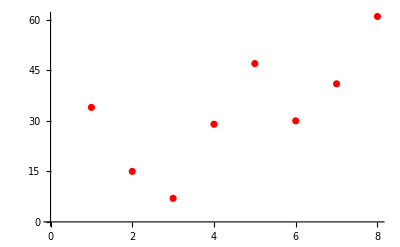

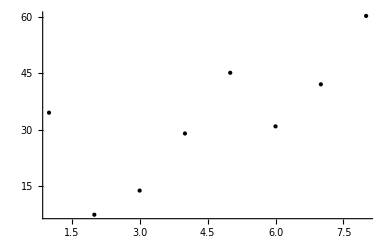

```mathematica
FindFit[dt,C ⅇ^Sin[p+t w] ((C1 P1[[t]])/E^(1+D1)+(C2 P2[[t]])/E^(1+D2)+(C3  P3[[t]])/E^(1+D3)),{p,w,C,C1,C2,C3},t]
Show[ListPlot[dt,PlotStyle->Red]]
Graphics[Point[Table[{t,C ⅇ^Sin[p+t w] ((C1 P1[[t]])/E^(1+D1)+(C2 P2[[t]])/E^(1+D2)+(C3  P3[[t]])/E^(1+D3))/.{p->2.8604548209689904,w->0.8113079358230999,C->2.394326821558768,C1->9.108017663123402,C2->3.8431188570952615,C3->-7.121924040523656}},{t,1,8}]],AspectRatio->1/GoldenRatio,Axes->True,PlotRange->All]
```

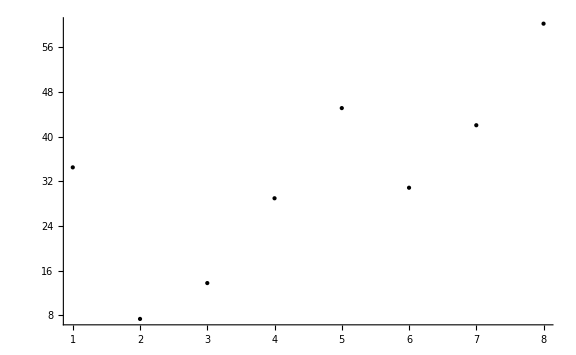

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression 1.00014 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression t cannot be used as a part specification.

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Part::pkspec1: The expression 1.00014 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

InterpolatingFunction[{{1, 8}}, <>]

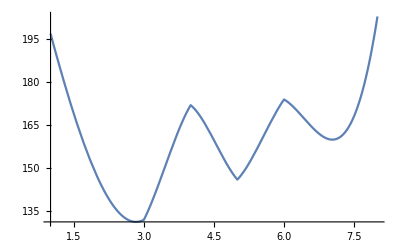

```mathematica
Show[%25,ImageSize->Large]
```